

```mathematica
Plot[x,{x,-2,2}]
```



```mathematica
Plot[x^2,{x,-2,2}]
```

```mathematica
FullSimplify[
Normalize@{x,x}.
Normalize@{x,x^2}
,x∈Reals]
```

(1+x)/(√2 √(1+x^2))

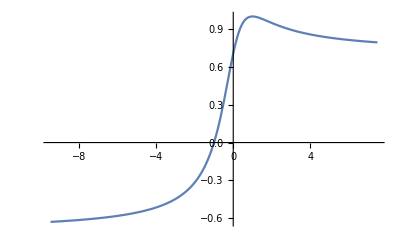

```mathematica
Plot[(1+x)/(√2 √(1+x^2)),{x,-9.493333333333336,7.493333333333335}]
```

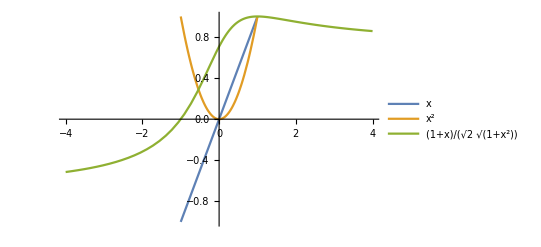

```mathematica
Plot[
{x,x^2,(1+x)/(√2 √(1+x^2))}
,{x,-4,4},PlotLegends->"Expressions",PlotRange->{-1,1}]
```

```mathematica
Reduce[x==x^2,x,Reals]
```

x==0||x==1

```mathematica
FullSimplify[
Normalize@{x,f[x]}.
Normalize@{x,g[x]}==(1+x)/(√2 √(1+x^2))
,{x,f[x],g[x]}∈Reals]
```

(x^2+f[x] g[x])/(√((x^2+f[x]^2) (x^2+g[x]^2)))==(1+x)/(√2 √(1+x^2))

```mathematica
FullSimplify[
Normalize@{x,x^3}.
Normalize@{x,g[x]}==(1+x)/(√2 √(1+x^2))
,{x,f[x],g[x]}∈Reals]
```

(Abs[x] (1+x g[x]))/(√((1+x^4) (x^2+g[x]^2)))==(1+x)/(√2 √(1+x^2))

```mathematica
(1+x)/(√2 √(1+x^2))==1
```

(1+x)/(√2 √(1+x^2))==1

```mathematica
Reduce[(1+x)/(√2 √(1+x^2))==1]
```

x==1

```mathematica
Solve[(Abs[x] (1+x g[x]))/(√((1+x^4) (x^2+g[x]^2)))==(1+x)/(√2 √(1+x^2)),g[x]]
```

{{g[x]→(-x (4+4 x^2) Abs[x]^2-√(x^2 (4+4 x^2)^2 Abs[x]^4-4 (-x^2-2 x^3-x^4-x^6-2 x^7-x^8+2 Abs[x]^2+2 x^2 Abs[x]^2) (-1-2 x-x^2-x^4-2 x^5-x^6+2 x^2 Abs[x]^2+2 x^4 Abs[x]^2)))/(2 (-1-2 x-x^2-x^4-2 x^5-x^6+2 x^2 Abs[x]^2+2 x^4 Abs[x]^2))},{g[x]→(-x (4+4 x^2) Abs[x]^2+√(x^2 (4+4 x^2)^2 Abs[x]^4-4 (-x^2-2 x^3-x^4-x^6-2 x^7-x^8+2 Abs[x]^2+2 x^2 Abs[x]^2) (-1-2 x-x^2-x^4-2 x^5-x^6+2 x^2 Abs[x]^2+2 x^4 Abs[x]^2)))/(2 (-1-2 x-x^2-x^4-2 x^5-x^6+2 x^2 Abs[x]^2+2 x^4 Abs[x]^2))}}

```mathematica
FullSimplify[
Solve[(Abs[x] (1+x g[x]))/(√((1+x^4) (x^2+g[x]^2)))==(1+x)/(√2 √(1+x^2)),g[x]]
,x∈Reals]
```

{{g[x]→-(2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))},{g[x]→(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))}}

```mathematica
-(2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))==(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))
```

-(2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))==(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))

```mathematica
Reduce[-(2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))==(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))]
```

x==-1||x==0||x==1||x==-1/(√2)+ⅈ Root-0.707Root[{-2+#1^2&,5+8 #1 #2+4 #2^2+4 #2^4&},{2,1}]-0.7071067811865476||x==-1/(√2)+ⅈ Root0.707Root[{-2+#1^2&,5-8 #1 #2+4 #2^2+4 #2^4&},{2,1}]0.7071067811865476||x==1/(√2)+ⅈ Root-0.707Root[{-2+#1^2&,5+8 #1 #2+4 #2^2+4 #2^4&},{2,1}]-0.7071067811865476||x==1/(√2)+ⅈ Root0.707Root[{-2+#1^2&,5-8 #1 #2+4 #2^2+4 #2^4&},{2,1}]0.7071067811865476

```mathematica
FullSimplify[
Solve[(Abs[x] (1+x g[x]))/(√((1+x^4) (x^2+g[x]^2)))==(1+x)/(√2 √(1+x^2)),g[x]]
,{x,g[x]}∈Reals]
```

{{g[x]→-(2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))},{g[x]→(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))}}

```mathematica
(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))
```

(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5))

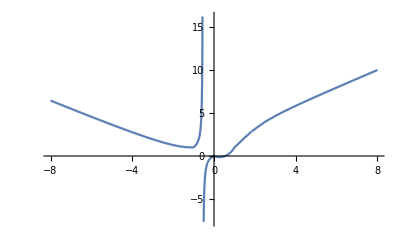

```mathematica
Plot[(-2 (x^3+x^5)+Abs[(-1+x) x (1+x) (1+x^4)])/(-1+x (-2-x+x^3-2 x^4+x^5)),{x,-8,8}]
```

```mathematica
Limit[(f[x-α]/f[x])^(1/α),α->0]
```

lim_(α→0) (f[x-α]/f[x])^(1/α)

```mathematica
x^3
```

x^3

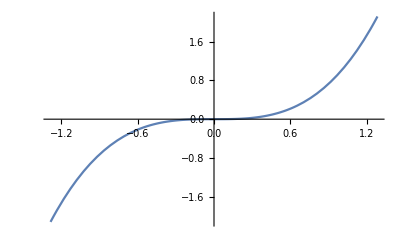

```mathematica
Plot[x^3,{x,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
1/(-f'[x])
```

-1/f'[x]

```mathematica
With[{f=Function[x,x^3]},
1/(-f'[x])
]
```

-1/(3 x^2)

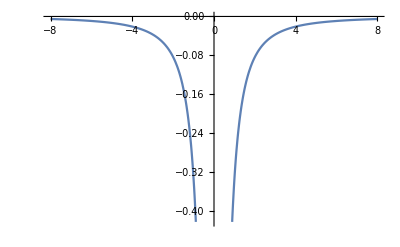

```mathematica
Plot[-1/(3 x^2),{x,-8,8}]
```